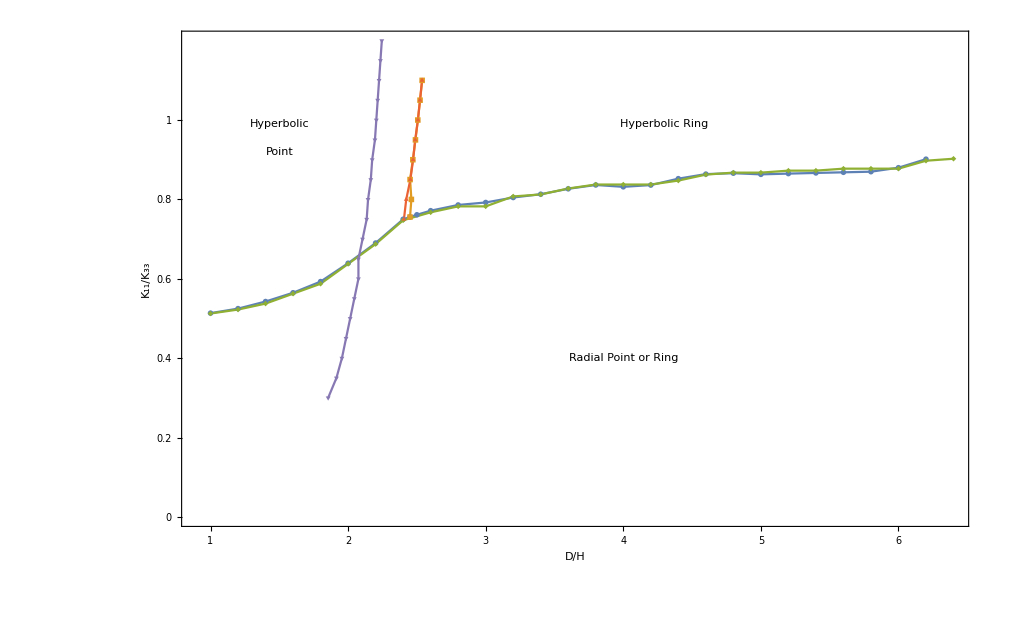

```mathematica
old1={{1,0.51345},{1.2,0.524834},{1.4,0.54271},{1.6,0.564809},{1.8,0.592971},{2,0.639201},{2.2,0.69013},{2.4,0.749939},{2.45, (0.761315+0.749939)/2},{2.5,0.761315},{2.6,0.771614},{2.8,0.786021},{3,0.792309},{3.2,0.804773},{3.4,0.81311},{3.6,0.826744},{3.8,0.836397},{4,0.831741},
{4.2, 0.836135},{4.4,0.852303},{4.6,0.863789},{4.8,0.866068},{5,0.863156},{5.2,0.865022},{5.4,0.866725},{5.6,0.868319},
{5.8,0.869846},{6,0.879924},{6.2,0.901416}};
old2={{2.45, (0.761315+0.749939)/2},{2.45986,0.8},{2.45048,0.85},{2.47049,0.9},{2.48962,0.95},{2.50661,1},{2.52297,1.05},{2.53818,1.1}};
new1={{1,0.5125},{1.2,0.5225},{1.4,0.5375},{1.6,0.5625},{1.8,0.5875},{2,0.6375},{2.2,0.6875},{2.4,0.7475},{2.6,0.7675},{2.8,0.7825},{3,0.7825},{3.2,0.8075},{3.4,0.8125},{3.6,0.8275},{3.8,0.8375},{4,0.8375},
{4.2, 0.8375},{4.4,0.8475},{4.6,0.8625},{4.8,0.8675},{5,0.8675},{5.2,0.8725},{5.4,0.8725},{5.6,0.8775},
{5.8,0.8775},{6,0.8775},{6.2,0.8975},{6.4,0.9025}
};
new2={{2.40575,0.75},{2.4225,0.8},{2.4525,0.85},{2.4725,0.9},{2.4875,0.95},{2.5075,1},{2.5225,1.05},{2.5375,1.1}};
new4={{2.605-0.75,0.3},{2.665-0.75, 0.35},{2.705-0.75,0.40},{2.735-0.75,0.45},{2.765-0.75,0.5},{2.795-0.75,0.55},{2.825-0.75,0.6},{2.825-0.75,0.65},{2.855-0.75,0.7},{2.885-0.75,0.75},{2.895-0.75,0.80},{2.915-0.75,0.85},{2.925-0.75,0.9},{2.945-0.75,0.95},{2.955-0.75,1.0},{2.965-0.75,1.05},{2.975-0.75,1.1},{2.985-0.75,1.15},{2.995-0.75,1.2}};
ListPlot[{old1,old2, new1,new2,new4},Joined->{True, True},PlotMarkers->{Automatic, Large}, PlotRange->{{0.9,6.4},Automatic},PlotStyle->{PointSize[0.02]}, Frame->{True, True, False, False}, FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},None},{{1,2,3,4,5,6},None}},LabelStyle->Large,FrameLabel->{{"K_11/K_33", None},{"D/H", None}},Epilog->{Text[Style["Hyperbolic",Large],{1.5,0.99}],Text[Style["Point",Large],{1.5,0.92}],Text[Style["Hyperbolic Ring",Large],{4.3,0.99}],Text[Style["Radial Point or Ring",Large],{4.0,0.4}]}]
```

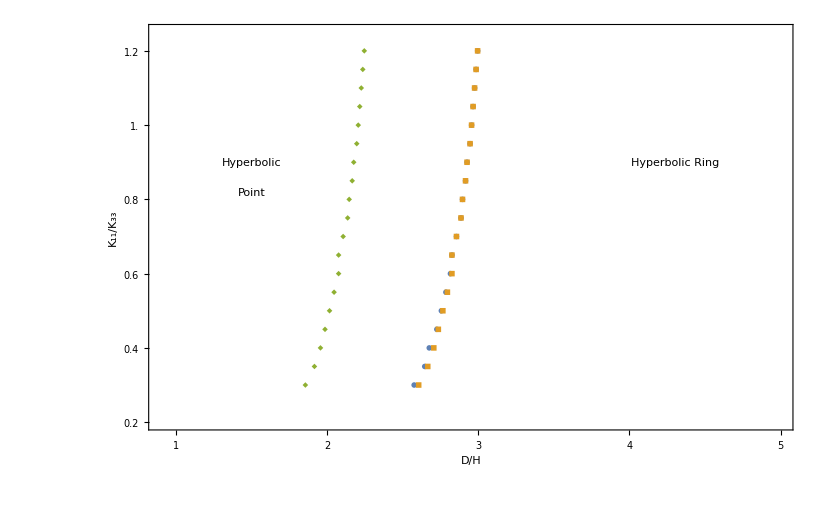

```mathematica
old3={{2.575,0.3},{2.645, 0.35},{2.675,0.40},{2.725,0.45},{2.755,0.5},{2.785,0.55},{2.815,0.6},{2.825,0.65},{2.855,0.7},{2.885,0.75},{2.895,0.80},{2.915,0.85},{2.925,0.9},{2.945,0.95},{2.955,1.0},{2.965,1.05},{2.975,1.1},{2.985,1.15},{2.995,1.2}};
new3={{2.605,0.3},{2.665, 0.35},{2.705,0.40},{2.735,0.45},{2.765,0.5},{2.795,0.55},{2.825,0.6},{2.825,0.65},{2.855,0.7},{2.885,0.75},{2.895,0.80},{2.915,0.85},{2.925,0.9},{2.945,0.95},{2.955,1.0},{2.965,1.05},{2.975,1.1},{2.985,1.15},{2.995,1.2}};
new4={{2.605-0.75,0.3},{2.665-0.75, 0.35},{2.705-0.75,0.40},{2.735-0.75,0.45},{2.765-0.75,0.5},{2.795-0.75,0.55},{2.825-0.75,0.6},{2.825-0.75,0.65},{2.855-0.75,0.7},{2.885-0.75,0.75},{2.895-0.75,0.80},{2.915-0.75,0.85},{2.925-0.75,0.9},{2.945-0.75,0.95},{2.955-0.75,1.0},{2.965-0.75,1.05},{2.975-0.75,1.1},{2.985-0.75,1.15},{2.995-0.75,1.2}};
ListPlot[{old3,new3,new4}, PlotMarkers->{Automatic, Medium},PlotRange->{{0.9,5},{0.2,1.25}},PlotStyle->PointSize[0.02], Frame->{True, True, False, False}, FrameTicks->{{{0.2,0.4,0.6,0.8,1.0,1.2},None},{{1,2,3,4,5},None}},LabelStyle->Large,FrameLabel->{{"K_11/K_33", None},{"D/H", None}},Epilog->{Text[Style["Hyperbolic",Large],{1.5,0.9}],Text[Style["Point",Large],{1.5,0.82}],Text[Style["Hyperbolic Ring",Large],{4.3,0.9}]}]
```

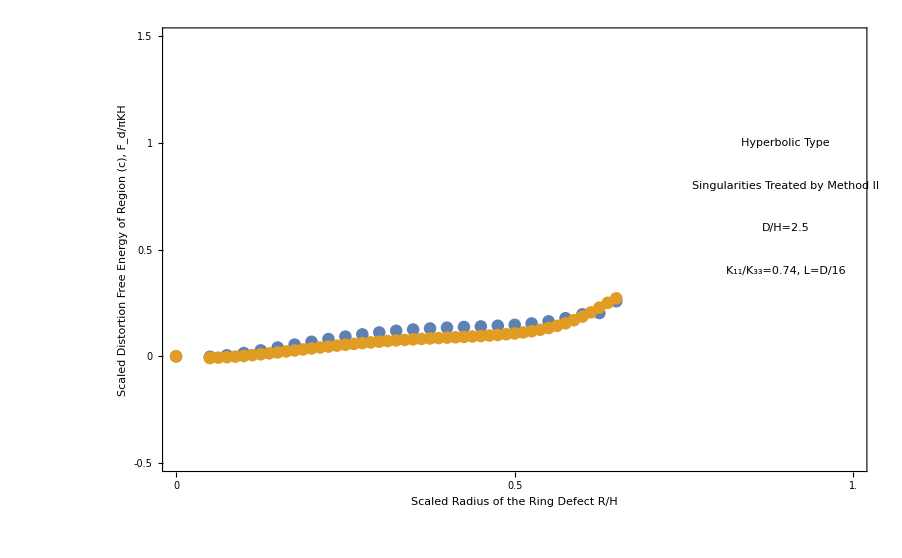

```mathematica
A25=
0.4×{{0,0},{0.125000,4.981381-4.988594},{0.125000,4.981381-4.988594},
{0.187500,5.000654-4.988594},{0.250000,5.027176-4.988594},{0.312500,5.058342-4.988594},
{0.375000,5.091874-4.988594},{0.437500,5.126024-4.988594},{0.500000,5.159441-4.988594},
{0.562500,5.191084-4.988594},{0.625000,5.220174-4.988594},{0.687500,5.246158-4.988594},
{0.750000,5.268694-4.988594},{0.812500,5.287646-4.988594},{0.875000,5.303079-4.988594},
{0.937500,5.315280-4.988594},{1.000000,5.324776-4.988594},{1.062500,5.332382-4.988594},
{1.125000,5.339251-4.988594},{1.187500,5.346961-4.988594},{1.250000,5.357602-4.988594},
{1.312500,5.373847-4.988594},{1.375000,5.398868-4.988594},{1.437500,5.435480-4.988594},
{1.500000,5.481368-4.988594},{1.562500,5.496533-4.988594},{1.625000,5.634995-4.988594}};


A25new=0.4×{{0,0},{0.125000,3.932789-3.951484},{0.125000,3.932789-3.951484},{0.156250,3.936357-3.951484},
{0.187500,3.941490-3.951484},{0.218750,3.948192-3.951484},{0.250000,3.956245-3.951484},{0.281250,3.965407-3.951484},
{0.312500,3.975445-3.951484},{0.343750,3.986148-3.951484},{0.375000,3.997328-3.951484},{0.406250,4.008814-3.951484},
{0.437500,4.020457-3.951484},{0.468750,4.032122-3.951484},{0.500000,4.043692-3.951484},{0.531250,4.055063-3.951484},
{0.562500,4.066144-3.951484},{0.593750,4.076859-3.951484},{0.625000,4.087143-3.951484},{0.656250,4.096945-3.951484},
{0.687500,4.106224-3.951484},{0.718750,4.114952-3.951484},{0.750000,4.123113-3.951484},{0.781250,4.130703-3.951484},
{0.812500,4.137730-3.951484},{0.843750,4.144217-3.951484},{0.875000,4.150199-3.951484},{0.906250,4.155725-3.951484},
{0.937500,4.160860-3.951484},{0.968750,4.165686-3.951484},{1.000000,4.170304-3.951484},{1.031250,4.174833-3.951484},
{1.062500,4.179418-3.951484},{1.093750,4.184226-3.951484},{1.125000,4.189455-3.951484},{1.156250,4.195335-3.951484},
{1.187500,4.202134-3.951484},{1.218750,4.210160-3.951484},{1.250000,4.219774-3.951484},{1.281250,4.231390-3.951484},
{1.312500,4.245486-3.951484},{1.343750,4.262609-3.951484},{1.375000,4.283383-3.951484},{1.406250,4.308501-3.951484},
{1.437500,4.338720-3.951484},{1.468750,4.374803-3.951484},{1.500000,4.417405-3.951484},{1.531250,4.466778-3.951484},
{1.562500,4.522060-3.951484},{1.593750,4.579576-3.951484},{1.625000,4.631657-3.951484}};
ListPlot[{A25,A25new},PlotStyle->PointSize[0.01], Frame->{True, True, False, False}, FrameTicks->{{{-0.5,0,0.5,1,1.5},None},{{0,0.5,1.0},None}}, PlotRange->{{0,1},{-0.5,1.5}},FrameLabel->{{"Scaled Distortion Free Energy of Region (c), F_d/πKH", None},{"Scaled Radius of the Ring Defect R/H", None}},PlotStyle->PointSize[0.01],LabelStyle->Large, Epilog->{Text[Style["Hyperbolic Type",Large],{0.9,1.0}],Text[Style["Singularities Treated by Method II",Large],{0.9,0.8}],Text[Style["D/H=2.5",Large],{0.9,0.6}],Text[Style["K_11/K_33=0.74, L=D/16",Large],{0.9,0.4}]}]
```

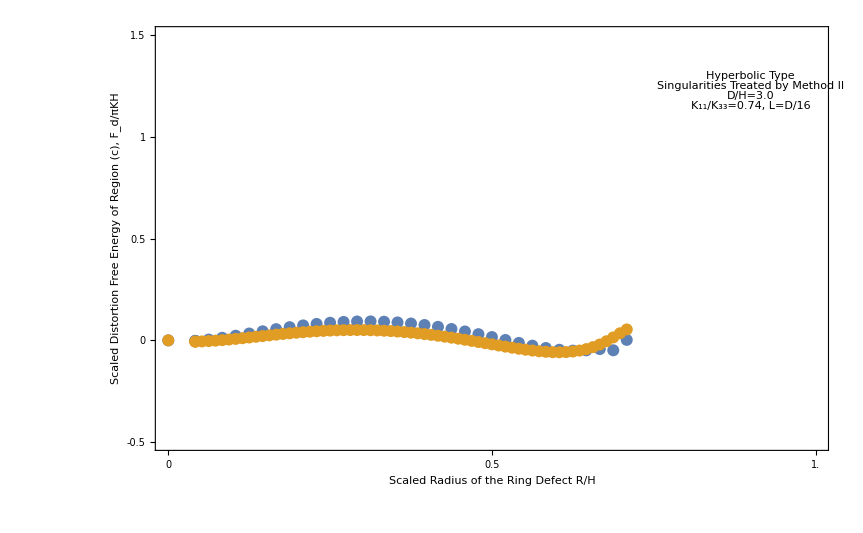

```mathematica
A3=
1/3×{{0,0},{0.125000,7.160203-7.167531},{0.125000,7.160203-7.167531},
{0.187500,7.179228-7.167531},{0.250000,7.205317-7.167531},{0.312500,7.235814-7.167531},
{0.375000,7.268374-7.167531},{0.437500,7.301170-7.167531},{0.500000,7.332753-7.167531},
{0.562500,7.361962-7.167531},{0.625000,7.387863-7.167531},{0.687500,7.409711-7.167531},
{0.750000,7.426920-7.167531},{0.812500,7.439042-7.167531},{0.875000,7.445748-7.167531},
{0.937500,7.446817-7.167531},{1.000000,7.442124-7.167531},{1.062500,7.431643-7.167531},
{1.125000,7.415439-7.167531},{1.187500,7.393681-7.167531},{1.250000,7.366649-7.167531},
{1.312500,7.334752-7.167531},{1.375000,7.298556-7.167531},{1.437500,7.258820-7.167531},
{1.500000,7.216544-7.167531},{1.562500,7.173037-7.167531},{1.625000,7.130001-7.167531},
{1.687500,7.089643-7.167531},{1.750000,7.054801-7.167531},{1.812500,7.029039-7.167531},
{1.875000,7.016539-7.167531},{1.937500,7.021017-7.167531},{2.000000,7.039646-7.167531},
{2.062500,7.021695-7.167531},{2.125000,7.174761-7.167531}};

A3new=1/3×{{0,0},{0.125000,5.747114-5.765959},{0.125000,5.747114-5.765959},{0.156250,5.750529-5.765959},
{0.187500,5.755451-5.765959},{0.218750,5.761878-5.765959},{0.250000,5.769584-5.765959},{0.281250,5.778316-5.765959},
{0.312500,5.787833-5.765959},{0.343750,5.797915-5.765959},{0.375000,5.808359-5.765959},{0.406250,5.818985-5.765959},
{0.437500,5.829629-5.765959},{0.468750,5.840141-5.765959},{0.500000,5.850386-5.765959},{0.531250,5.860243-5.765959},
{0.562500,5.869600-5.765959},{0.593750,5.878358-5.765959},{0.625000,5.886428-5.765959},{0.656250,5.893728-5.765959},
{0.687500,5.900187-5.765959},{0.718750,5.905742-5.765959},{0.750000,5.910337-5.765959},{0.781250,5.913924-5.765959},
{0.812500,5.916462-5.765959},{0.843750,5.917916-5.765959},{0.875000,5.918260-5.765959},{0.906250,5.917471-5.765959},
{0.937500,5.915536-5.765959},{0.968750,5.912444-5.765959},{1.000000,5.908194-5.765959},{1.031250,5.902789-5.765959},
{1.062500,5.896238-5.765959},{1.093750,5.888557-5.765959},{1.125000,5.879771-5.765959},{1.156250,5.869907-5.765959},
{1.187500,5.859004-5.765959},{1.218750,5.847106-5.765959},{1.250000,5.834267-5.765959},{1.281250,5.820550-5.765959},
{1.312500,5.806029-5.765959},{1.343750,5.790787-5.765959},{1.375000,5.774921-5.765959},{1.406250,5.758543-5.765959},
{1.437500,5.741779-5.765959},{1.468750,5.724773-5.765959},{1.500000,5.707692-5.765959},{1.531250,5.690722-5.765959},
{1.562500,5.674079-5.765959},{1.593750,5.658006-5.765959},{1.625000,5.642783-5.765959},{1.656250,5.628732-5.765959},
{1.687500,5.616217-5.765959},{1.718750,5.605660-5.765959},{1.750000,5.597542-5.765959},{1.781250,5.592419-5.765959},
{1.812500,5.590924-5.765959},{1.843750,5.593785-5.765959},{1.875000,5.601824-5.765959},{1.906250,5.615966-5.765959},
{1.937500,5.637216-5.765959},{1.968750,5.666605-5.765959},{2.000000,5.705049-5.765959},{2.031250,5.752992-5.765959},
{2.062500,5.809549-5.765959},{2.093750,5.870444-5.765959},{2.125000,5.926901-5.765959}};

ListPlot[{A3,A3new},PlotStyle->PointSize[0.01], Frame->{True, True, False, False}, FrameTicks->{{{-0.5,0,0.5,1,1.5},None},{{0,0.5,1.0},None}}, PlotRange->{{0,1},{-0.5,1.5}},FrameLabel->{{"Scaled Distortion Free Energy of Region (c), F_d/πKH", None},{"Scaled Radius of the Ring Defect R/H", None}},PlotStyle->PointSize[0.01],LabelStyle->Large, Epilog->{Text[Style["Hyperbolic Type",Large],{0.9,1.3}],Text[Style["Singularities Treated by Method II",Large],{0.9,1.25}],Text[Style["D/H=3.0",Large],{0.9,1.2}],Text[Style["K_11/K_33=0.74, L=D/16",Large],{0.9,1.15}]}]
```

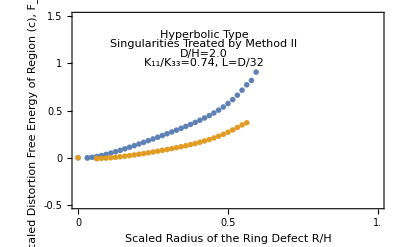

```mathematica
A2=
0.5×{{0,0},{0.062500,3.915059-3.917716},{0.062500,3.915059-3.917716},
{0.093750,3.926855-3.917716},{0.125000,3.943760-3.917716},{0.156250,3.964762-3.917716},
{0.187500,3.988980-3.917716},{0.218750,4.015756-3.917716},{0.250000,4.044588-3.917716},
{0.281250,4.075083-3.917716},{0.312500,4.106922-3.917716},{0.343750,4.139851-3.917716},
{0.375000,4.173664-3.917716},{0.406250,4.208194-3.917716},{0.437500,4.243316-3.917716},
{0.468750,4.278934-3.917716},{0.500000,4.314988-3.917716},{0.531250,4.351449-3.917716},
{0.562500,4.388323-3.917716},{0.593750,4.425648-3.917716},{0.625000,4.463500-3.917716},
{0.656250,4.501997-3.917716},{0.687500,4.541299-3.917716},{0.718750,4.581621-3.917716},
{0.750000,4.623234-3.917716},{0.781250,4.666481-3.917716},{0.812500,4.711785-3.917716},
{0.843750,4.759670-3.917716},{0.875000,4.810776-3.917716},{0.906250,4.865887-3.917716},
{0.937500,4.925965-3.917716},{0.968750,4.992180-3.917716},{1.000000,5.065940-3.917716},
{1.031250,5.148891-3.917716},{1.062500,5.242758-3.917716},{1.093750,5.348582-3.917716},
{1.125000,5.462989-3.917716},{1.156250,5.554079-3.917716},{1.187500,5.731642-3.917716}};

A2new=0.5×{{0,0},{0.125000,2.592523-2.610649},{0.125000,2.592523-2.610649},{0.156250,2.596671-2.610649},
{0.187500,2.602594-2.610649},{0.218750,2.610326-2.610649},{0.250000,2.619681-2.610649},{0.281250,2.630447-2.610649},
{0.312500,2.642430-2.610649},{0.343750,2.655459-2.610649},{0.375000,2.669390-2.610649},{0.406250,2.684103-2.610649},
{0.437500,2.699503-2.610649},{0.468750,2.715521-2.610649},{0.500000,2.732108-2.610649},{0.531250,2.749242-2.610649},
{0.562500,2.766925-2.610649},{0.593750,2.785186-2.610649},{0.625000,2.804080-2.610649},{0.656250,2.823692-2.610649},
{0.687500,2.844142-2.610649},{0.718750,2.865585-2.610649},{0.750000,2.888213-2.610649},{0.781250,2.912265-2.610649},
{0.812500,2.938029-2.610649},{0.843750,2.965842-2.610649},{0.875000,2.996097-2.610649},{0.906250,3.029241-2.610649},
{0.937500,3.065753-2.610649},{0.968750,3.106114-2.610649},{1.000000,3.150700-2.610649},{1.031250,3.199554-2.610649},
{1.062500,3.251828-2.610649},{1.093750,3.304436-2.610649},{1.125000,3.350812-2.610649}};
ListPlot[{A2,A2new},PlotStyle->PointSize[0.01], Frame->{True, True, False, False}, FrameTicks->{{{-0.5,0,0.5,1,1.5},None},{{0,0.5,1.0},None}}, PlotRange->{{0,1},{-0.5,1.5}}, FrameLabel->{{"Scaled Distortion Free Energy of Region (c), F_d/πKH", None},{"Scaled Radius of the Ring Defect R/H", None}},PlotStyle->PointSize[0.01],LabelStyle->Large, Epilog->{Text[Style["Hyperbolic Type",Large],{0.42,1.3}],Text[Style["Singularities Treated by Method II",Large],{0.42,1.2}],Text[Style["D/H=2.0",Large],{0.42,1.1}],Text[Style["K_11/K_33=0.74, L=D/32",Large],{0.42,1}]}]
```

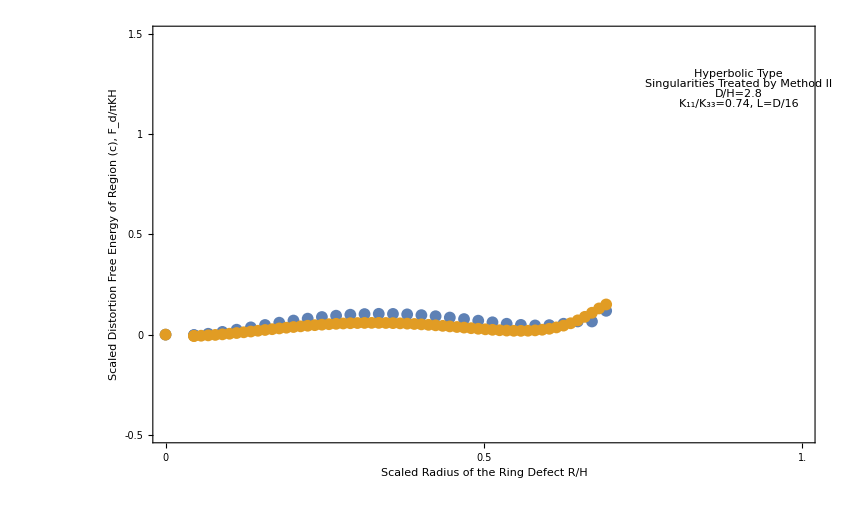

```mathematica
A28=
5/14×{{0,0},{0.125000,6.257815-6.264896},{0.125000,6.257815-6.264896},
{0.187500,6.276887-6.264896},{0.250000,6.303091-6.264896},{0.312500,6.333761-6.264896},
{0.375000,6.366566-6.264896},{0.437500,6.399700-6.264896},{0.500000,6.431737-6.264896},
{0.562500,6.461544-6.264896},{0.625000,6.488224-6.264896},{0.687500,6.511076-6.264896},
{0.750000,6.529573-6.264896},{0.812500,6.543336-6.264896},{0.875000,6.552125-6.264896},
{0.937500,6.555832-6.264896},{1.000000,6.554473-6.264896},{1.062500,6.548200-6.264896},
{1.125000,6.537305-6.264896},{1.187500,6.522246-6.264896},{1.250000,6.503672-6.264896},
{1.312500,6.482469-6.264896},{1.375000,6.459816-6.264896},{1.437500,6.437264-6.264896},
{1.500000,6.416835-6.264896},{1.562500,6.401132-6.264896},{1.625000,6.393428-6.264896},
{1.687500,6.397567-6.264896},{1.750000,6.416977-6.264896},{1.812500,6.449188-6.264896},
{1.875000,6.448629-6.264896},{1.937500,6.597862-6.264896}};


A28new=5/14×{{0,0},{0.125000,4.999914-5.018628},{0.125000,4.999914-5.018628},{0.156250,5.003366-5.018628},
{0.187500,5.008346-5.018628},{0.218750,5.014849-5.018628},{0.250000,5.022649-5.018628},{0.281250,5.031496-5.018628},
{0.312500,5.041151-5.018628},{0.343750,5.051394-5.018628},{0.375000,5.062028-5.018628},{0.406250,5.072873-5.018628},
{0.437500,5.083769-5.018628},{0.468750,5.094571-5.018628},{0.500000,5.105148-5.018628},{0.531250,5.115381-5.018628},
{0.562500,5.125166-5.018628},{0.593750,5.134408-5.018628},{0.625000,5.143022-5.018628},{0.656250,5.150936-5.018628},
{0.687500,5.158084-5.018628},{0.718750,5.164412-5.018628},{0.750000,5.169873-5.018628},{0.781250,5.174428-5.018628},
{0.812500,5.178049-5.018628},{0.843750,5.180713-5.018628},{0.875000,5.182407-5.018628},{0.906250,5.183124-5.018628},
{0.937500,5.182867-5.018628},{0.968750,5.181646-5.018628},{1.000000,5.179480-5.018628},{1.031250,5.176396-5.018628},
{1.062500,5.172432-5.018628},{1.093750,5.167634-5.018628},{1.125000,5.162058-5.018628},{1.156250,5.155774-5.018628},
{1.187500,5.148861-5.018628},{1.218750,5.141415-5.018628},{1.250000,5.133545-5.018628},{1.281250,5.125379-5.018628},
{1.312500,5.117061-5.018628},{1.343750,5.108760-5.018628},{1.375000,5.100669-5.018628},{1.406250,5.093008-5.018628},
{1.437500,5.086029-5.018628},{1.468750,5.080025-5.018628},{1.500000,5.075327-5.018628},{1.531250,5.072318-5.018628},
{1.562500,5.071438-5.018628},{1.593750,5.073193-5.018628},{1.625000,5.078160-5.018628},{1.656250,5.087002-5.018628},{1.687500,5.100470-5.018628},
{1.718750,5.119405-5.018628},{1.750000,5.144720-5.018628},{1.781250,5.177349-5.018628},
{1.812500,5.218114-5.018628},{1.843750,5.267387-5.018628},{1.875000,5.324291-5.018628},
{1.906250,5.384763-5.018628},{1.937500,5.440384-5.018628}};
ListPlot[{A28,A28new},PlotStyle->PointSize[0.01], Frame->{True, True, False, False}, FrameTicks->{{{-0.5,0,0.5,1,1.5},None},{{0,0.5,1.0},None}}, PlotRange->{{0,1},{-0.5,1.5}}, FrameLabel->{{"Scaled Distortion Free Energy of Region (c), F_d/πKH", None},{"Scaled Radius of the Ring Defect R/H", None}},PlotStyle->PointSize[0.01],LabelStyle->Large, Epilog->{Text[Style["Hyperbolic Type",Large],{0.9,1.3}],Text[Style["Singularities Treated by Method II",Large],{0.9,1.25}],Text[Style["D/H=2.8",Large],{0.9,1.20}],Text[Style["K_11/K_33=0.74, L=D/16",Large],{0.9,1.15}]}]
```

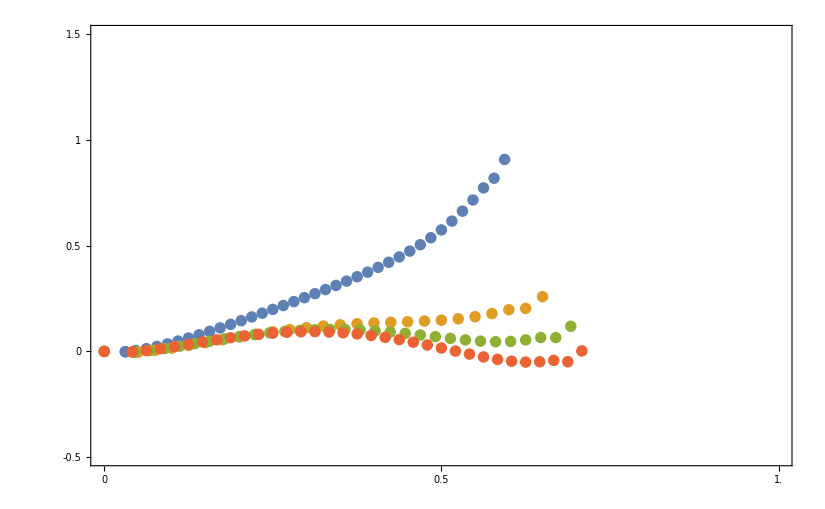

```mathematica
ListPlot[{A2,A25,A28,A3},PlotStyle->PointSize[0.01], Frame->{True, True, False, False}, FrameTicks->{{{-0.5,0,0.5,1,1.5},None},{{0,0.5,1.0},None}}, PlotRange->{{0,1},{-0.5,1.5}}]
```

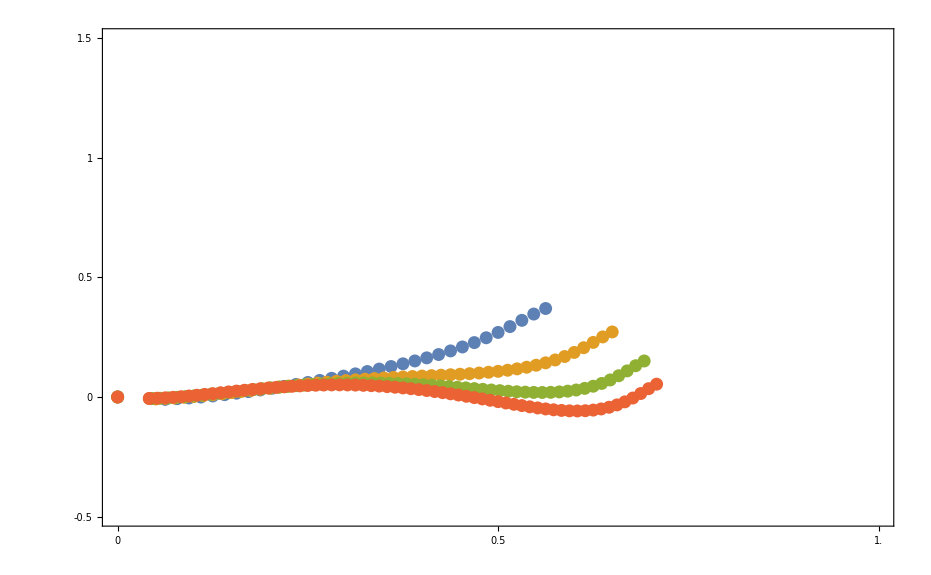

```mathematica
ListPlot[{A2new,A25new,A28new,A3new},PlotStyle->PointSize[0.01], Frame->{True, True, False, False}, FrameTicks->{{{-0.5,0,0.5,1,1.5},None},{{0,0.5,1.0},None}}, PlotRange->{{0,1},{-0.5,1.5}}]
```